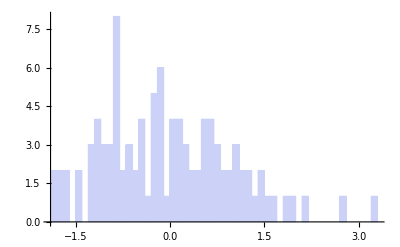

```mathematica
n=100;
x = RandomVariate[NormalDistribution[0, 1],n];
tHit= RandomVariate[NormalDistribution[0, 1],n];
tHit=Table[0,{i,1,n}];
bin={0.1};
Histogram[x,bin]
```

```mathematica
dt1= RandomVariate[NormalDistribution[0, 0.1],n];
dt2= RandomVariate[NormalDistribution[0, 0.1],n];
t1=Table[tHit[[i]]+x[[i]]+dt1[[i]],{i,1,n}];
t2=Table[tHit[[i]]+10-x[[i]]+dt2[[i]],{i,1,n}];
t1t2=Table[{t1[[i]],t2[[i]]},{i,1,n}];
St=Table[t1[[i]]+t2[[i]],{i,1,n}];
tD=Table[t1[[i]]-t2[[i]],{i,1,n}];
```

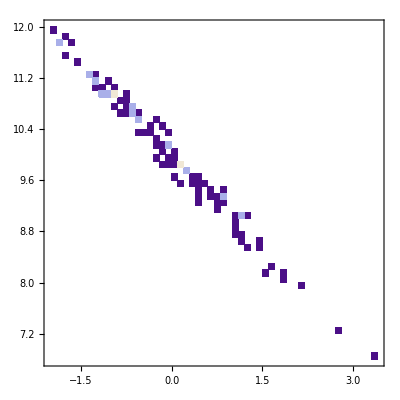

```mathematica
t1t2plot=DensityHistogram[t1t2,{0.1}]
```

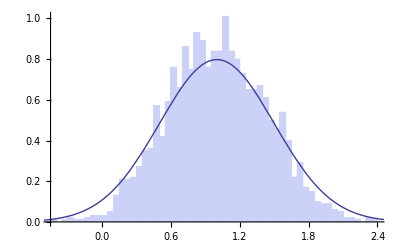

```mathematica
Show[
Histogram[St,{0.05},"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,0.5],x],{x,-2,3}]
]
```

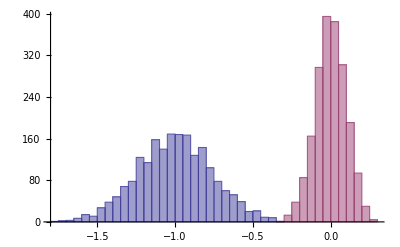

```mathematica
Histogram[{tD,dt1},{0.05}]
```

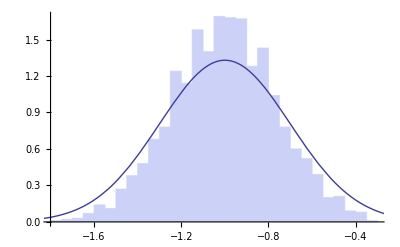

```mathematica
Show[
Histogram[tD,{0.05},"ProbabilityDensity"],
Plot[PDF[NormalDistribution[-1,0.3],x],{x,-2,0.5}]
]
```

```mathematica
LinearModelFit[t1t2,t,t]["CorrelationMatrix"]
LinearModelFit[t1t2,t,t]["CovarianceMatrix"]
LinearModelFit[t1t2,t,t]["ParameterTable"]
LinearModelFit[t1t2,t,t]["ParameterConfidenceIntervalTable"]
LinearModelFit[t1t2,t,t][{"RSquared","AdjustedRSquared"}]
LinearModelFit[t1t2,t,t]["ANOVATable"]
LinearModelFit[t1t2,t,t]["ANOVATableSumsOfSquares"]/LinearModelFit[t1t2,t,t]["ANOVATableDegreesOfFreedom"]
RootMeanSquare[LinearModelFit[t1t2,t,t]["FitResiduals"]]
RootMeanSquare[LinearModelFit[t1t2,t,t]["StandardizedResiduals"]]
RootMeanSquare[LinearModelFit[t1t2,t,t]["StudentizedResiduals"]]
```

{{1.,0.0239678},{0.0239678,1.}}

{{0.000195262,4.44497×10^-6},{4.44497×10^-6,0.000176142}}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.98819 | 0.0139736 | 714.789 | 5.77865×10^-184
t | -0.979714 | 0.0132718 | -73.8189 | 1.04553×10^-87

| Estimate | Standard Error | Confidence Interval
1 | 9.98819 | 0.0139736 | {9.96046,10.0159}
t | -0.979714 | 0.0132718 | {-1.00605,-0.953376}

{0.982334,0.982153}

| DF | SS | MS | F-Statistic | P-Value
t | 1 | 106.342 | 106.342 | 5449.23 | 1.04553×10^-87
Error | 98 | 1.91247 | 0.019515 |  | 
Total | 99 | 108.254 |  |  |

{106.342,0.019515,1.09348}

0.138292

0.998994

1.00835

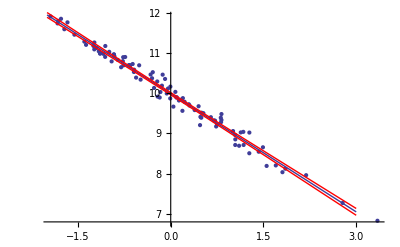

```mathematica
Show[
ListPlot[t1t2],
Plot[Normal[Gfit],{t,-2,3}],
Plot[Evaluate[LinearModelFit[t1t2,t,t]["MeanPredictionBands"]],{t,-2,3},PlotStyle->{Red}]
]
```